```mathematica
ClearAll["Global`*"]
$Assumptions=β∈Reals&&Ω∈Reals&&Ω0∈Reals&&t∈Reals&&β>0 && Ω>0 &&t>0&&β<π/4&&ωL∈Reals&& ωL>0&&A∈Reals&&A>0&&B∈Reals&&B>0&& m∈PositiveIntegers&&k∈PositiveIntegers;
```

```mathematica
Build time evolution operator including off-resonant driving and perpendicular component
First full solution (HTilde0/HTilde1), then approximation (H0a/H1a). Define both electronic subspaces.
Replace Cos/Sin[phi] with Cos/Sin[ϕ0+(m-1)*A*τ] in H0 and with Cos/Sin[ϕ1+(n-1)*A*τ]in H1 for the DDrf protocol.
```

```mathematica
(*Hamiltonian in the lab frame, H0 (H1) is nuclear spin Hamiltonian in electron spin-0 (electron spin-1) subspace, Hd denotes driving field*)
H0=ωL/2*PauliMatrix[3]+Ω*Cos[ω*t +ϕ]*PauliMatrix[1];
H1=ω1/2*(Sin[β]*PauliMatrix[1]+Cos[β]*PauliMatrix[3])+Ω*Cos[β]*Cos[ω*t +ϕ]*(Cos[β]*PauliMatrix[1]-Sin[β]*PauliMatrix[3])+Ω*Sin[β]*Cos[ω*t +ϕ]*(Sin[β]*PauliMatrix[1]+Cos[β]*PauliMatrix[3]);
(*unitary transformation*)
U=MatrixExp[ⅈ*ω/2*t(Sin[β]*PauliMatrix[1]+Cos[β]*PauliMatrix[3])];
UDag =MatrixExp[-ⅈ*ω/2*t(Sin[β]*PauliMatrix[1]+Cos[β]*PauliMatrix[3])];
H0Tilde0=FullSimplify[U.H0.UDag];
H1Tilde0=FullSimplify[U.H1.UDag];
H0Tilde= H0Tilde0-ω/2(Sin[β]*PauliMatrix[1]+Cos[β]*PauliMatrix[3])//TrigExpand;
H1Tilde=H1Tilde0-ω/2(Sin[β]*PauliMatrix[1]+Cos[β]*PauliMatrix[3])//TrigExpand;
H0Tilde=H0Tilde/.{Cos[β]->(ωL-A)/Sqrt[B^2+(ωL-A)^2],Sin[β]->B/Sqrt[B^2+(ωL-A)^2], ω1->Sqrt[B^2+(ωL-A)^2]};
H1Tilde=H1Tilde/.{Cos[β]->(ωL-A)/Sqrt[B^2+(ωL-A)^2],Sin[β]->B/Sqrt[B^2+(ωL-A)^2], ω1->Sqrt[B^2+(ωL-A)^2]};
H0Tilde=FullSimplify[H0Tilde];
H1Tilde=FullSimplify[H1Tilde];
```

```mathematica
H0Tilde/.{ϕ->ϕ0+(m-1)*A*τ,Ω->Ω0}//MatrixForm
H1Tilde/.ϕ->ϕ1+(n-1)*A*τ//MatrixForm
```

(((A-ωL) (A^2 √(B^2+(-A+ωL)^2)+B^2 √(B^2+(-A+ωL)^2)+A ωL (√(B^2+(A-ωL)^2)-2 √(B^2+(-A+ωL)^2))+ωL^2 (-√(B^2+(A-ωL)^2)+√(B^2+(-A+ωL)^2)))+B √(B^2+(A-ωL)^2) (Ω (A-ωL) Cos[A (-1+m) τ+ϕ0]+B ωL Cos[t √(B^2+(-A+ωL)^2)]+Ω (A-ωL) (-2 Cos[A (-1+m) τ+ϕ0+t √(B^2+(-A+ωL)^2)]+Cos[A (-1+m) τ+ϕ0+2 t √(B^2+(-A+ωL)^2)])))/(2 (B^2+(A-ωL)^2)^(3/2)) | (-B √(B^2+(A-ωL)^2) √(B^2+(-A+ωL)^2)+B (A-ωL) ωL (-1+Cos[t √(B^2+(-A+ωL)^2)])+2 B^2 Ω Cos[A (-1+m) τ+ϕ0+t √(B^2+(-A+ωL)^2)]+Ω (A-ωL)^2 Cos[A (-1+m) τ+ϕ0+2 t √(B^2+(-A+ωL)^2)]-ⅈ B √(B^2+(A-ωL)^2) ωL Sin[t √(B^2+(-A+ωL)^2)]+2 ⅈ A Ω √(B^2+(A-ωL)^2) Sin[A (-1+m) τ+ϕ0] Sin[t √(B^2+(-A+ωL)^2)]^2-2 ⅈ Ω √(B^2+(A-ωL)^2) ωL Sin[A (-1+m) τ+ϕ0] Sin[t √(B^2+(-A+ωL)^2)]^2+Ω (A-ωL) Cos[A (-1+m) τ+ϕ0] (A-ωL-ⅈ √(B^2+(A-ωL)^2) Sin[2 t √(B^2+(-A+ωL)^2)]))/(2 (B^2+(A-ωL)^2))
(-B √(B^2+(A-ωL)^2) √(B^2+(-A+ωL)^2)+B (A-ωL) ωL (-1+Cos[t √(B^2+(-A+ωL)^2)])+2 B^2 Ω Cos[A (-1+m) τ+ϕ0+t √(B^2+(-A+ωL)^2)]+Ω (A-ωL)^2 Cos[A (-1+m) τ+ϕ0+2 t √(B^2+(-A+ωL)^2)]+ⅈ B √(B^2+(A-ωL)^2) ωL Sin[t √(B^2+(-A+ωL)^2)]-2 ⅈ A Ω √(B^2+(A-ωL)^2) Sin[A (-1+m) τ+ϕ0] Sin[t √(B^2+(-A+ωL)^2)]^2+2 ⅈ Ω √(B^2+(A-ωL)^2) ωL Sin[A (-1+m) τ+ϕ0] Sin[t √(B^2+(-A+ωL)^2)]^2+Ω (A-ωL) Cos[A (-1+m) τ+ϕ0] (A-ωL+ⅈ √(B^2+(A-ωL)^2) Sin[2 t √(B^2+(-A+ωL)^2)]))/(2 (B^2+(A-ωL)^2)) | -(B^2 ωL Cos[t √(B^2+(-A+ωL)^2)]+(A-ωL) ((A-ωL) ωL+√(B^2+(A-ωL)^2) √(B^2+(-A+ωL)^2)-4 B Ω Cos[A (-1+m) τ+ϕ0+t √(B^2+(-A+ωL)^2)] Sin[1/2 t √(B^2+(-A+ωL)^2)]^2))/(2 (B^2+(A-ωL)^2)))

(-((A-ωL) ((B^2+(A-ωL)^2) (√(B^2+(A-ωL)^2)-√(B^2+(-A+ωL)^2))+4 B Ω √(B^2+(A-ωL)^2) Cos[A (-1+n) τ+ϕ1+t √(B^2+(-A+ωL)^2)] Sin[1/2 t √(B^2+(-A+ωL)^2)]^2))/(2 (B^2+(A-ωL)^2)^(3/2)) | (B (B^2+(A-ωL)^2) (√(B^2+(A-ωL)^2)-√(B^2+(-A+ωL)^2))+2 Ω Cos[A (-1+n) τ+ϕ1+t √(B^2+(-A+ωL)^2)] (B^2 √(B^2+(A-ωL)^2)+√(B^2+(A-ωL)^2) (A-ωL)^2 Cos[t √(B^2+(-A+ωL)^2)]-ⅈ (B^2+(A-ωL)^2) (A-ωL) Sin[t √(B^2+(-A+ωL)^2)]))/(2 (B^2+(A-ωL)^2)^(3/2))
(B (B^2+(A-ωL)^2) (√(B^2+(A-ωL)^2)-√(B^2+(-A+ωL)^2))+2 Ω Cos[A (-1+n) τ+ϕ1+t √(B^2+(-A+ωL)^2)] (B^2 √(B^2+(A-ωL)^2)+√(B^2+(A-ωL)^2) (A-ωL)^2 Cos[t √(B^2+(-A+ωL)^2)]+ⅈ (B^2+(A-ωL)^2) (A-ωL) Sin[t √(B^2+(-A+ωL)^2)]))/(2 (B^2+(A-ωL)^2)^(3/2)) | ((A-ωL) ((B^2+(A-ωL)^2) (√(B^2+(A-ωL)^2)-√(B^2+(-A+ωL)^2))+4 B Ω √(B^2+(A-ωL)^2) Cos[A (-1+n) τ+ϕ1+t √(B^2+(-A+ωL)^2)] Sin[1/2 t √(B^2+(-A+ωL)^2)]^2))/(2 (B^2+(A-ωL)^2)^(3/2)))

```mathematica
(*Now define time evolution operator as function*)
U0f[t_,m_,ϕ0_]:=MatrixExp[-ⅈ*t*({{((A-ωL) (A^2 √(B^2+(-A+ωL)^2)+B^2 √(B^2+(-A+ωL)^2)+A ωL (√(B^2+(A-ωL)^2)-2 √(B^2+(-A+ωL)^2))+ωL^2 (-√(B^2+(A-ωL)^2)+√(B^2+(-A+ωL)^2)))+B √(B^2+(A-ωL)^2) (Ω (A-ωL) Cos[A (-1+m) τ+ϕ0]+B ωL Cos[t √(B^2+(-A+ωL)^2)]+Ω (A-ωL) (-2 Cos[A (-1+m) τ+ϕ0+t √(B^2+(-A+ωL)^2)]+Cos[A (-1+m) τ+ϕ0+2 t √(B^2+(-A+ωL)^2)])))/(2 (B^2+(A-ωL)^2)^(3/2)), (-B √(B^2+(A-ωL)^2) √(B^2+(-A+ωL)^2)+B (A-ωL) ωL (-1+Cos[t √(B^2+(-A+ωL)^2)])+2 B^2 Ω Cos[A (-1+m) τ+ϕ0+t √(B^2+(-A+ωL)^2)]+Ω (A-ωL)^2 Cos[A (-1+m) τ+ϕ0+2 t √(B^2+(-A+ωL)^2)]-ⅈ B √(B^2+(A-ωL)^2) ωL Sin[t √(B^2+(-A+ωL)^2)]+2 ⅈ A Ω √(B^2+(A-ωL)^2) Sin[A (-1+m) τ+ϕ0] Sin[t √(B^2+(-A+ωL)^2)]^2-2 ⅈ Ω √(B^2+(A-ωL)^2) ωL Sin[A (-1+m) τ+ϕ0] Sin[t √(B^2+(-A+ωL)^2)]^2+Ω (A-ωL) Cos[A (-1+m) τ+ϕ0] (A-ωL-ⅈ √(B^2+(A-ωL)^2) Sin[2 t √(B^2+(-A+ωL)^2)]))/(2 (B^2+(A-ωL)^2))}, {(-B √(B^2+(A-ωL)^2) √(B^2+(-A+ωL)^2)+B (A-ωL) ωL (-1+Cos[t √(B^2+(-A+ωL)^2)])+2 B^2 Ω Cos[A (-1+m) τ+ϕ0+t √(B^2+(-A+ωL)^2)]+Ω (A-ωL)^2 Cos[A (-1+m) τ+ϕ0+2 t √(B^2+(-A+ωL)^2)]+ⅈ B √(B^2+(A-ωL)^2) ωL Sin[t √(B^2+(-A+ωL)^2)]-2 ⅈ A Ω √(B^2+(A-ωL)^2) Sin[A (-1+m) τ+ϕ0] Sin[t √(B^2+(-A+ωL)^2)]^2+2 ⅈ Ω √(B^2+(A-ωL)^2) ωL Sin[A (-1+m) τ+ϕ0] Sin[t √(B^2+(-A+ωL)^2)]^2+Ω (A-ωL) Cos[A (-1+m) τ+ϕ0] (A-ωL+ⅈ √(B^2+(A-ωL)^2) Sin[2 t √(B^2+(-A+ωL)^2)]))/(2 (B^2+(A-ωL)^2)), -(B^2 ωL Cos[t √(B^2+(-A+ωL)^2)]+(A-ωL) ((A-ωL) ωL+√(B^2+(A-ωL)^2) √(B^2+(-A+ωL)^2)-4 B Ω Cos[A (-1+m) τ+ϕ0+t √(B^2+(-A+ωL)^2)] Sin[1/2 t √(B^2+(-A+ωL)^2)]^2))/(2 (B^2+(A-ωL)^2))}})];
U1f[t_,n_,ϕ1_] :=MatrixExp[-ⅈ*t*({{-((A-ωL) ((B^2+(A-ωL)^2) (√(B^2+(A-ωL)^2)-√(B^2+(-A+ωL)^2))+4 B Ω √(B^2+(A-ωL)^2) Cos[A (-1+n) τ+ϕ1+t √(B^2+(-A+ωL)^2)] Sin[1/2 t √(B^2+(-A+ωL)^2)]^2))/(2 (B^2+(A-ωL)^2)^(3/2)), (B (B^2+(A-ωL)^2) (√(B^2+(A-ωL)^2)-√(B^2+(-A+ωL)^2))+2 Ω Cos[A (-1+n) τ+ϕ1+t √(B^2+(-A+ωL)^2)] (B^2 √(B^2+(A-ωL)^2)+√(B^2+(A-ωL)^2) (A-ωL)^2 Cos[t √(B^2+(-A+ωL)^2)]-ⅈ (B^2+(A-ωL)^2) (A-ωL) Sin[t √(B^2+(-A+ωL)^2)]))/(2 (B^2+(A-ωL)^2)^(3/2))}, {(B (B^2+(A-ωL)^2) (√(B^2+(A-ωL)^2)-√(B^2+(-A+ωL)^2))+2 Ω Cos[A (-1+n) τ+ϕ1+t √(B^2+(-A+ωL)^2)] (B^2 √(B^2+(A-ωL)^2)+√(B^2+(A-ωL)^2) (A-ωL)^2 Cos[t √(B^2+(-A+ωL)^2)]+ⅈ (B^2+(A-ωL)^2) (A-ωL) Sin[t √(B^2+(-A+ωL)^2)]))/(2 (B^2+(A-ωL)^2)^(3/2)), ((A-ωL) ((B^2+(A-ωL)^2) (√(B^2+(A-ωL)^2)-√(B^2+(-A+ωL)^2))+4 B Ω √(B^2+(A-ωL)^2) Cos[A (-1+n) τ+ϕ1+t √(B^2+(-A+ωL)^2)] Sin[1/2 t √(B^2+(-A+ωL)^2)]^2))/(2 (B^2+(A-ωL)^2)^(3/2))}})];
```

```mathematica
H0a=((ωL*Cos[β]-ω)*Cos[β]-Ω0*Sin[β]*Cos[β]*Cos[ϕ0+(m-1)*A*τ])/2*PauliMatrix[3]+(-ω*Sin[β]+ωL*Cos[β]*Sin[β]+Ω0*(Cos[β])^2*Cos[ϕ0+(m-1)*A*τ])/2*PauliMatrix[1]+(Ω0*Cos[β]*Sin[ϕ0+(m-1)*A*τ])/2*PauliMatrix[2]/.{Cos[β]->(ωL-A)/Sqrt[B^2+(ωL-A)^2],Sin[β]->B/Sqrt[B^2+(ωL-A)^2], ω1->Sqrt[B^2+(ωL-A)^2]};
H1a=((ω1-ω)*Cos[β]-Ω*Cos[β]*Sin[β]*Cos[ϕ1+(n-1)*A*τ])/2*PauliMatrix[3]+((ω1-ω)*Sin[β]+Ω*(Cos[β])^2*Cos[ϕ1+(n-1)*A*τ])/2*PauliMatrix[1]+(Ω*Cos[β]*Sin[ϕ1+(n-1)*A*τ])/2*PauliMatrix[2]/.{Cos[β]->(ωL-A)/Sqrt[B^2+(ωL-A)^2],Sin[β]->B/Sqrt[B^2+(ωL-A)^2], ω1->Sqrt[B^2+(ωL-A)^2]};
H0a //MatrixForm;
H1a //MatrixForm;
```

```mathematica
(*Now define time evolution operator as function*)
U0a[t_,m_,ϕ0_]:=MatrixExp[-ⅈ*({{1/2 (((-A+ωL) (-ω+(ωL (-A+ωL))/(√(B^2+(-A+ωL)^2))))/(√(B^2+(-A+ωL)^2))-(B Ω0 (-A+ωL) Cos[A (-1+m) τ+ϕ0])/(B^2+(-A+ωL)^2)), 1/2 ((B ωL (-A+ωL))/(B^2+(-A+ωL)^2)-(B ω)/(√(B^2+(-A+ωL)^2))+(Ω0 (-A+ωL)^2 Cos[A (-1+m) τ+ϕ0])/(B^2+(-A+ωL)^2))-(ⅈ Ω0 (-A+ωL) Sin[A (-1+m) τ+ϕ0])/(2 √(B^2+(-A+ωL)^2))}, {1/2 ((B ωL (-A+ωL))/(B^2+(-A+ωL)^2)-(B ω)/(√(B^2+(-A+ωL)^2))+(Ω0 (-A+ωL)^2 Cos[A (-1+m) τ+ϕ0])/(B^2+(-A+ωL)^2))+(ⅈ Ω0 (-A+ωL) Sin[A (-1+m) τ+ϕ0])/(2 √(B^2+(-A+ωL)^2)), 1/2 (-((-A+ωL) (-ω+(ωL (-A+ωL))/(√(B^2+(-A+ωL)^2))))/(√(B^2+(-A+ωL)^2))+(B Ω0 (-A+ωL) Cos[A (-1+m) τ+ϕ0])/(B^2+(-A+ωL)^2))}})*t];
U1a[t_,n_,ϕ1_] :=MatrixExp[-ⅈ*({{1/2 (((-A+ωL) (-ω+√(B^2+(-A+ωL)^2)))/(√(B^2+(-A+ωL)^2))-(B Ω (-A+ωL) Cos[A (-1+n) τ+ϕ1])/(B^2+(-A+ωL)^2)), 1/2 ((B (-ω+√(B^2+(-A+ωL)^2)))/(√(B^2+(-A+ωL)^2))+(Ω (-A+ωL)^2 Cos[A (-1+n) τ+ϕ1])/(B^2+(-A+ωL)^2))-(ⅈ Ω (-A+ωL) Sin[A (-1+n) τ+ϕ1])/(2 √(B^2+(-A+ωL)^2))}, {1/2 ((B (-ω+√(B^2+(-A+ωL)^2)))/(√(B^2+(-A+ωL)^2))+(Ω (-A+ωL)^2 Cos[A (-1+n) τ+ϕ1])/(B^2+(-A+ωL)^2))+(ⅈ Ω (-A+ωL) Sin[A (-1+n) τ+ϕ1])/(2 √(B^2+(-A+ωL)^2)), 1/2 (-((-A+ωL) (-ω+√(B^2+(-A+ωL)^2)))/(√(B^2+(-A+ωL)^2))+(B Ω (-A+ωL) Cos[A (-1+n) τ+ϕ1])/(B^2+(-A+ωL)^2))}})*t];
```

```mathematica
Next, build operator sequence. Depending on which solution should be computed:
```

```mathematica
U2V0a[t_,n_,ϕ1_, m_,ϕ0_]:=U1a[t,n,ϕ1].U0a[t,m,ϕ0];
U2V1a[t_,m_,ϕ0_, n_,ϕ1_]:=U0a[t,m,ϕ0].U1a[t,n,ϕ1];
```

```mathematica
U2V0f[t_,n_,ϕ1_, m_,ϕ0_]:=U1f[t,n,ϕ1].U0f[t,m,ϕ0];
U2V1f[t_,m_,ϕ0_, n_,ϕ1_]:=U0f[t,m,ϕ0].U1f[t,n,ϕ1];
```

```mathematica
(*#################################################################################*)
(*#################################################################################*)
```

```mathematica
(*first test: in case of no off-resonant driving and no perpendicular component, do we get a CNOT? -> we do. It was the entire calculation below with B=0.*)
(*so now, it is possible to look at the fidelty for different values of B*)
M=4;
Ω0=Ω;
ω=Sqrt[B^2+(ωL-A)^2];
```

```mathematica
(*Version with full model*)
V0tablef=Table[U2V0f[2*τ,i,0,i-1,π],{i,M,4,-2}]/.{τ->π/(2*M*Ω)};
PrependTo[V0tablef,U0f[τ,M+1, π]/.{τ->π/(2*M*Ω)}];
AppendTo[V0tablef,U1f[2*τ,2,0]/.{τ->π/(2*M*Ω)}];
AppendTo[V0tablef,U0f[τ,1,π]/.{τ->π/(2*M*Ω)}];
V0tablef;
V0f=Dot @@ V0tablef ;
V1tablef=Table[U2V1f[2*τ,i,0,i-1,π],{i,M,4,-2}]/.{τ->π/(2*M*Ω)};
PrependTo[V1tablef,U1f[τ,M+1, π]/.{τ->π/(2*M*Ω)}];
AppendTo[V1tablef,U0f[2*τ,2,0]/.{τ->π/(2*M*Ω)}];
AppendTo[V1tablef,U1f[τ,1,π]/.{τ->π/(2*M*Ω)}];
V1tablef;
V1f=Dot @@ V1tablef;

VORf=KroneckerProduct[{{1,0},{0,0}},V0f]+KroneckerProduct[{{0,0},{0,1}},V1f];
VZf=KroneckerProduct[IdentityMatrix[2],MatrixExp[-PauliMatrix[3]*ⅈ*(N*A*τg)/2]]/.τg->π/(2*N*Ω);
VZf†=FullSimplify[ConjugateTranspose[VZf], Assumptions->{A ∈ Reals,Ω∈ Reals}];

VcnotORf=Exp[-ⅈ*π/4]*KroneckerProduct[IdentityMatrix[2],MatrixExp[PauliMatrix[1]*ⅈ*π/4]].KroneckerProduct[MatrixExp[PauliMatrix[3]*ⅈ*π/4],IdentityMatrix[2]].VZf†.VORf;
Ucnot={{1,0,0,0},{0,1,0,0},{0,0,0,1},{0,0,1,0}};
```

```mathematica
Favf=(Abs[Tr[Ucnot.VcnotORf]]^2+4)/20/.{τ->π/(2*M*Ω),A->20,B->0,ωL->1980};
```

```mathematica
FavBf=(Abs[Tr[Ucnot.VcnotORf]]^2+4)/20/.{τ->π/(2*M*Ω),A->20,B->20,ωL->1980};
```

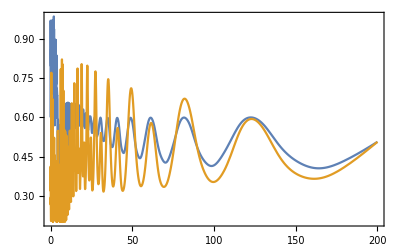

```mathematica
Plot[{Favf,FavBf},{Ω,0,200},Frame->True]
```

```mathematica
(*Version with RWA*)
V0tablea=Table[U2V0a[2*τ,i,0,i-1,π],{i,M,4,-2}]/.{τ->π/(2*M*Ω)};
PrependTo[V0tablea,U0a[τ,M+1, π]/.{τ->π/(2*M*Ω)}];
AppendTo[V0tablea,U1a[2*τ,2,0]/.{τ->π/(2*M*Ω)}];
AppendTo[V0tablea,U0a[τ,1,π]/.{τ->π/(2*M*Ω)}];
V0tablea;
V0a=Dot @@ V0tablea ;
V1tablea=Table[U2V1a[2*τ,i,0,i-1,π],{i,M,4,-2}]/.{τ->π/(2*M*Ω)};
PrependTo[V1tablea,U1a[τ,M+1, π]/.{τ->π/(2*M*Ω)}];
AppendTo[V1tablea,U0a[2*τ,2,0]/.{τ->π/(2*M*Ω)}];
AppendTo[V1tablea,U1a[τ,1,π]/.{τ->π/(2*M*Ω)}];
V1tablea;
V1a=Dot @@ V1tablea;

VORa=KroneckerProduct[{{1,0},{0,0}},V0a]+KroneckerProduct[{{0,0},{0,1}},V1a];
VZa=KroneckerProduct[IdentityMatrix[2],MatrixExp[-PauliMatrix[3]*ⅈ*(N*A*τg)/2]]/.τg->π/(2*N*Ω);
VZa†=FullSimplify[ConjugateTranspose[VZa], Assumptions->{A ∈ Reals,Ω∈ Reals}];

VcnotORa=Exp[-ⅈ*π/4]*KroneckerProduct[IdentityMatrix[2],MatrixExp[PauliMatrix[1]*ⅈ*π/4]].KroneckerProduct[MatrixExp[PauliMatrix[3]*ⅈ*π/4],IdentityMatrix[2]].VZa†.VORa;
Ucnot={{1,0,0,0},{0,1,0,0},{0,0,0,1},{0,0,1,0}};
```

```mathematica
Fava=(Abs[Tr[Ucnot.VcnotORa]]^2+4)/20/.{τ->π/(2*M*Ω),A->20,B->0,ωL->1980};
FavBa=(Abs[Tr[Ucnot.VcnotORa]]^2+4)/20/.{τ->π/(2*M*Ω),A->20,B->20,ωL->1980};
```

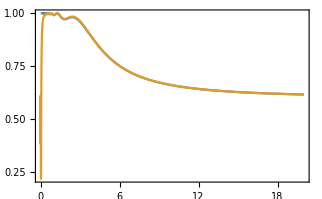

```mathematica
Plot[{Fava,FavBa},{Ω,0,20},Frame->True]
```

```mathematica
Fav2dplot=(Abs[Tr[Ucnot.VcnotOR]]^2+4)/20/.{τ->π/(2*M*Ω),A->190,ωL->430};
DensityPlot[Fav2dplot,{B,0,20},{Ω,0,100},PlotLegends->Automatic,AxesLabel->{Ω,B}]
```

```mathematica
(*test: do we get correct dynamics with B=0?*)
H0check=((ωL*Cos[β]-ω)*Cos[β]-Ω0*Sin[β]*Cos[β]*Cos[ϕ0+(m-1)*A*τ])/2*PauliMatrix[3]+(-ω*Sin[β]+ωL*Cos[β]*Sin[β]+Ω0*(Cos[β])^2*Cos[ϕ0+(m-1)*A*τ])/2*PauliMatrix[1]+(Ω0*Cos[β]*Sin[ϕ0+(m-1)*A*τ])/2*PauliMatrix[2]/.{ω->ωL-A,Cos[β]->1,Sin[β]->0, ω1->ωL-A};
H1check=((ω1-ω)*Cos[β]-Ω*Cos[β]*Sin[β]*Cos[ϕ1+(n-1)*A*τ])/2*PauliMatrix[3]+((ω1-ω)*Sin[β]+Ω*(Cos[β])^2*Cos[ϕ1+(n-1)*A*τ])/2*PauliMatrix[1]+(Ω*Cos[β]*Sin[ϕ1+(n-1)*A*τ])/2*PauliMatrix[2]/.{ω->ωL-A,Cos[β]->1,Sin[β]->0, ω1->ωL-A};
H0check //MatrixForm
H1check //MatrixForm
(*passt!*)
```

(A/2 | 0
0 | -A/2)

(0 | 1/2 Ω Cos[A (-1+n) τ+ϕ1]-1/2 ⅈ Ω Sin[A (-1+n) τ+ϕ1]
1/2 Ω Cos[A (-1+n) τ+ϕ1]+1/2 ⅈ Ω Sin[A (-1+n) τ+ϕ1] | 0)